```mathematica
Table[Binomial[k,2],{k,1,10}]
```

{0,1,3,6,10,15,21,28,36,45}

```mathematica
Table[StirlingS2[k,2],{k,1,10}]
```

{0,1,3,7,15,31,63,127,255,511}

```mathematica
Table[{Binomial[n,2],3n-6},{n,5,10}]
```

{{10,9},{15,12},{21,15},{28,18},{36,21},{45,24}}

```mathematica
Simplify[Binomial[n,2]-(3n-6)]
```

1/2 (12-7 n+n^2)

```mathematica
Solve[1/2 (12-7 n+n^2)==0,n]
```

{{n→3},{n→4}}

```mathematica
Table[1/2 (12-7 n+n^2),{n,5,10}]
```

{1,3,6,10,15,21}

```mathematica
ChromaticPolynomial[JacobsThalGraph[4],3]
```

6

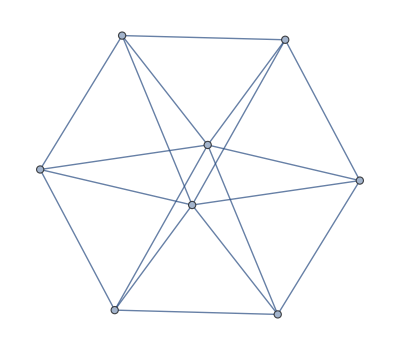

```mathematica
JacobsThalGraph[4]
```

```mathematica
FormulaForm[form_]:=Sort[Tally[Map[SymbolLevel[#]&,form]]]
```

```mathematica
FormulaForm[FindFullFormula[JacobsThalGraph[2]]]
```

{{3,1},{4,3},{5,3},{6,1}}

```mathematica
TableForm[Table[FormulaForm[FindFullFormula[MinimalGraph[k]]],{k,3,8}],TableDepth->2]
```

{4,1} |  |  |  |  | 
{4,1} | {5,1} |  |  |  | 
{4,1} | {5,3} | {6,1} |  |  | 
{4,1} | {5,7} | {6,6} | {7,1} |  | 
{4,1} | {5,15} | {6,25} | {7,10} | {8,1} | 
{4,1} | {5,31} | {6,90} | {7,65} | {8,15} | {9,1}

```mathematica
TableForm[Table[FormulaForm[FindFullFormula[JacobsThalGraph[k]]],{k,3,8}],TableDepth->2]
```

{4,5} | {5,10} | {6,6} | {7,1} |  |  |  |  |  | 
{3,1} | {4,11} | {5,30} | {6,29} | {7,10} | {8,1} |  |  |  | 
{4,21} | {5,91} | {6,126} | {7,70} | {8,15} | {9,1} |  |  |  | 
{3,1} | {4,43} | {5,273} | {6,525} | {7,420} | {8,146} | {9,21} | {10,1} |  | 
{4,85} | {5,820} | {6,2142} | {7,2331} | {8,1170} | {9,273} | {10,28} | {11,1} |  | 
{3,1} | {4,171} | {5,2460} | {6,8653} | {7,12390} | {8,8427} | {9,2835} | {10,470} | {11,36} | {12,1}

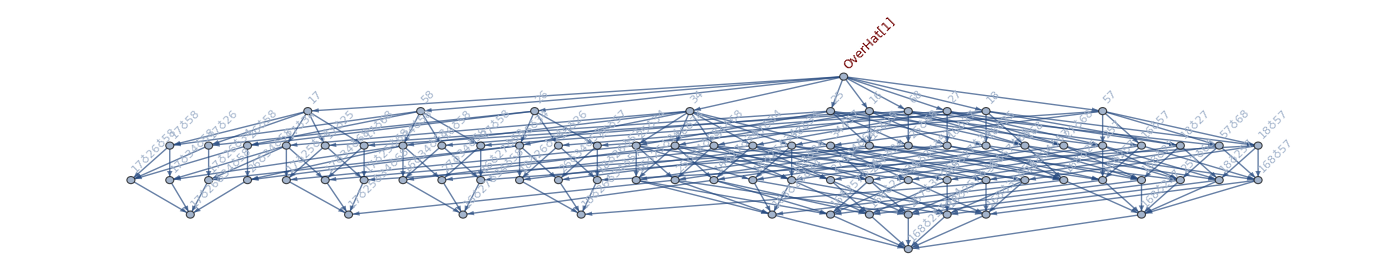

```mathematica
TableForm[Table[FormulaGraphReverse2[Fold[Plus,FindFullFormula[JacobsThalGraph[k]]]],
{k,4,4}]]
```

## Barely four colorable

```mathematica
CompFromPart[count_,part_]:=Block[{result={}, g=CompleteGraph[count],current=0,vertices},
vertices=VertexList[g];
Table[
result=Append[result,EdgeList[VertexDelete[g,Take[vertices,p-Length[vertices]]]]];
g=VertexDelete[g,Take[vertices,p]];
vertices=Take[vertices,p-Length[vertices]];
,
{p,part}
];
result
]
```

```mathematica
ListSols3[count_]:=Block[{parts=Map[Reverse,IntegerPartitions[count,{4}]], comp,g},
Table[
comp=Flatten[CompFromPart[count,part]];
Print [comp];
g=CompleteGraph[count];
EdgeDelete[
CompleteGraph[count,
GraphLayout->"RadialEmbedding",
EdgeStyle->Map[#->{Thick,Red}&,comp],
EdgeLabels->{First[EdgeList[g]]->Style[Framed[Length[comp],Background->White],Darker[Green],Bold,14],
Last[EdgeList[g]]->Style[Framed[EdgeCount[g],Background->White],Blue,Bold,14]},
VertexStyle->Red,
VertexLabels->"Name"
],
comp]
,
{part, parts}
]
]
```

```mathematica
ListSols4[count_]:=Block[{parts=Map[Reverse,IntegerPartitions[count,{3}]], comp,g},
Table[
comp=Flatten[CompFromPart[count,part]];
g=CompleteGraph[count];
EdgeDelete[
CompleteGraph[count,
GraphLayout->"RadialEmbedding",
EdgeStyle->Map[#->{Thick,Red}&,comp],
EdgeLabels->{First[EdgeList[g]]->Style[Framed[Length[comp],Background->White],Darker[Green],Bold,14],
Last[EdgeList[g]]->Style[Framed[EdgeCount[g],Background->White],Blue,Bold,14]},
VertexStyle->Red,
VertexLabels->"Name"
],
comp]
,
{part, parts}
]
]
```

{3<->4,3<->5,3<->6,3<->7,4<->5,4<->6,4<->7,5<->6,5<->7,6<->7}

{2<->3,4<->5,4<->6,4<->7,5<->6,5<->7,6<->7}

{2<->3,2<->4,3<->4,5<->6,5<->7,6<->7}

{1<->2,3<->4,5<->6,5<->7,6<->7}

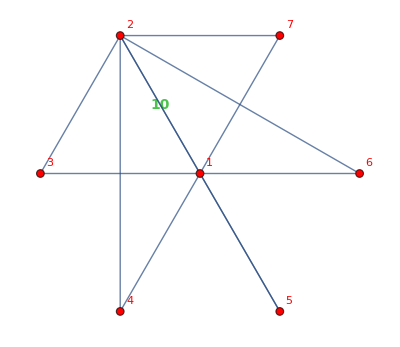
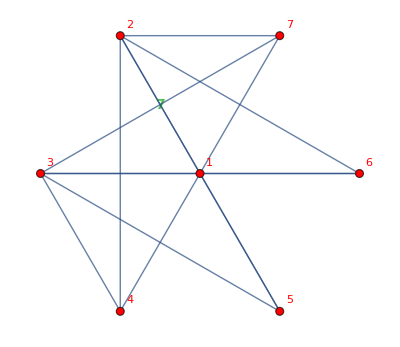
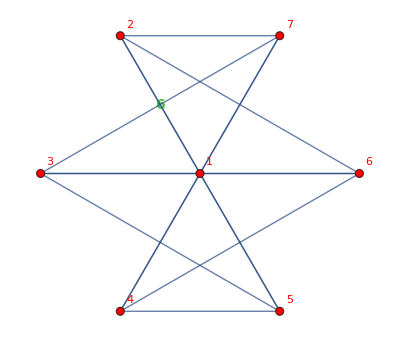
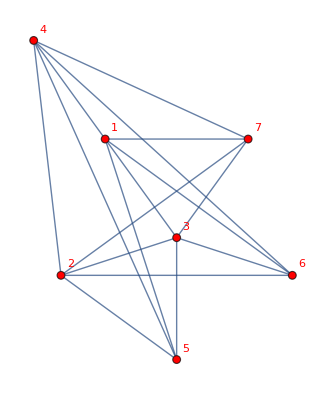

```mathematica
ListSols4[7]
```

```mathematica
TableForm[Map[Map[Last,#]&,Map[FormulaLevels[FindFullFormula[#]]&,BarelyFourColorableGraphsOfCount[8]]],TableDepth->2]
```

1 | 15 | 25 | 10 | 1
1 | 8 | 13 | 7 | 1
1 | 6 | 11 | 6 | 1
1 | 5 | 8 | 5 | 1
1 | 4 | 6 | 4 | 1

```mathematica
TableForm[Map[Map[Last,#]&,Map[FormulaLevels[FindFullFormula[#]]&,BarelyFourColorableGraphsOfCount[9]]],TableDepth->2]
```

1 | 31 | 90 | 65 | 15 | 1
1 | 16 | 40 | 35 | 11 | 1
1 | 10 | 28 | 26 | 9 | 1
1 | 9 | 21 | 20 | 8 | 1
1 | 7 | 17 | 17 | 7 | 1
1 | 6 | 13 | 13 | 6 | 1

```mathematica
TableForm[Map[Map[Last,#]&,Map[FormulaLevels[FindFullFormula[#]]&,BarelyFourColorableGraphsOfCount[10]]],TableDepth->2]
```

1 | 63 | 301 | 350 | 140 | 21 | 1
1 | 32 | 121 | 155 | 80 | 16 | 1
1 | 18 | 71 | 100 | 56 | 13 | 1
1 | 17 | 56 | 75 | 46 | 12 | 1
1 | 14 | 61 | 86 | 50 | 12 | 1
1 | 11 | 38 | 54 | 35 | 10 | 1
1 | 10 | 30 | 41 | 28 | 9 | 1
1 | 9 | 30 | 45 | 30 | 9 | 1
1 | 8 | 24 | 34 | 24 | 8 | 1

```mathematica
TableForm[Map[Map[Last,#]&,Map[FormulaLevels[FindFullFormula[#]]&,BarelyFourColorableGraphsOfCount[11]]],TableDepth->2]
```

1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1
1 | 64 | 364 | 651 | 490 | 161 | 22 | 1
1 | 34 | 184 | 366 | 300 | 111 | 18 | 1
1 | 33 | 153 | 276 | 235 | 96 | 17 | 1
1 | 22 | 136 | 276 | 236 | 92 | 16 | 1
1 | 19 | 89 | 171 | 156 | 69 | 14 | 1
1 | 18 | 73 | 131 | 121 | 58 | 13 | 1
1 | 15 | 75 | 147 | 136 | 62 | 13 | 1
1 | 13 | 59 | 120 | 115 | 54 | 12 | 1
1 | 12 | 49 | 92 | 89 | 45 | 11 | 1
1 | 10 | 39 | 75 | 75 | 39 | 10 | 1

```mathematica
IntegerPartitions[10,{4}]
```

{{7,1,1,1},{6,2,1,1},{5,3,1,1},{5,2,2,1},{4,4,1,1},{4,3,2,1},{4,2,2,2},{3,3,3,1},{3,3,2,2}}

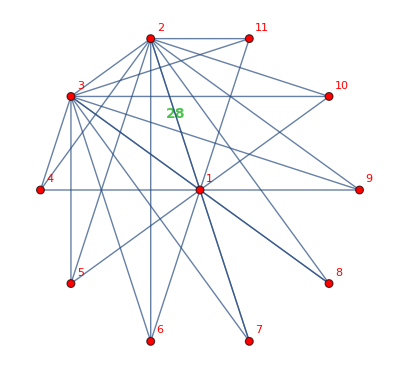
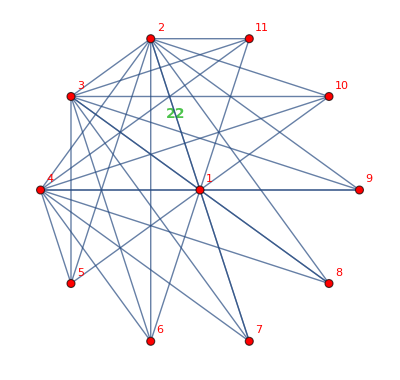
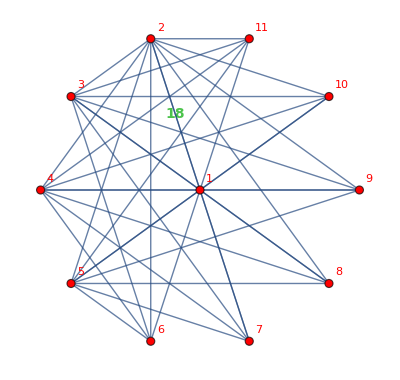
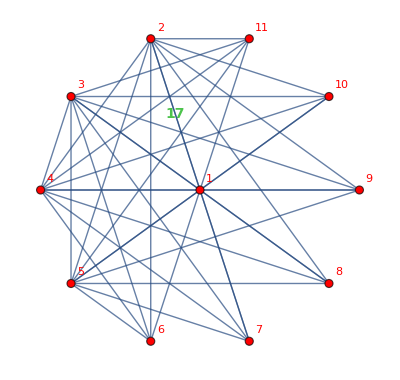
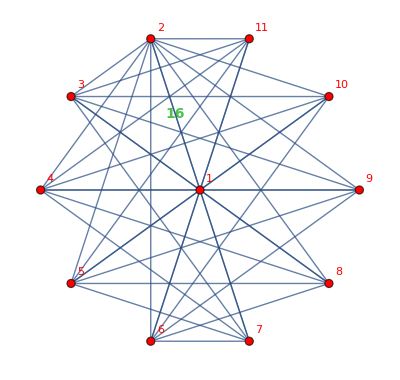
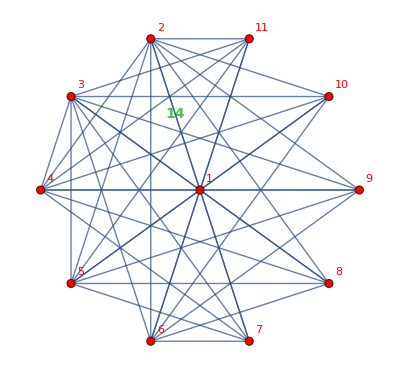
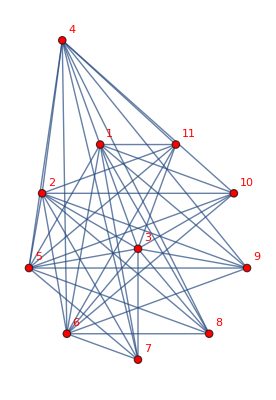
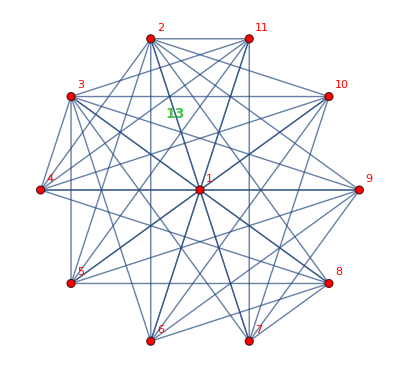

```mathematica
BarelyFourColorableGraphsOfCount[11]
```

```mathematica
FillSideDiagonal[mat_]:=Block[{i,l=Length[mat],res},
res=Normal[mat];
For[i=1,i<=l,i++,
res[[i,Mod[i,l]+1]]=1;
res[[i,Mod[i-2,l]+1]]=1
];
res
]
```

```mathematica
Map[Normal[#]&,ListSols4[7]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

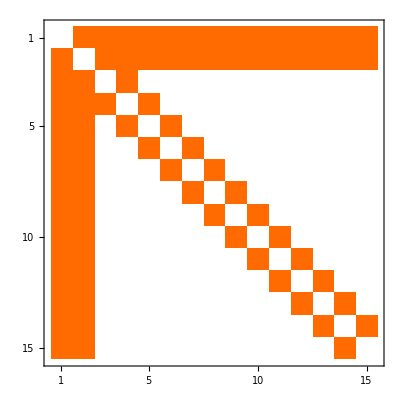
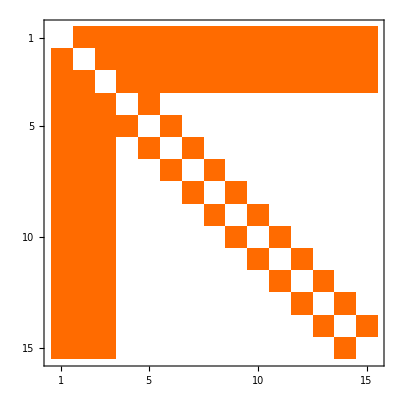
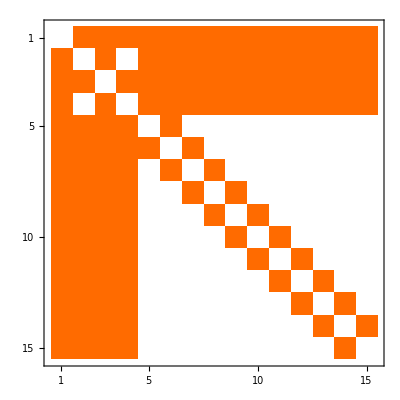
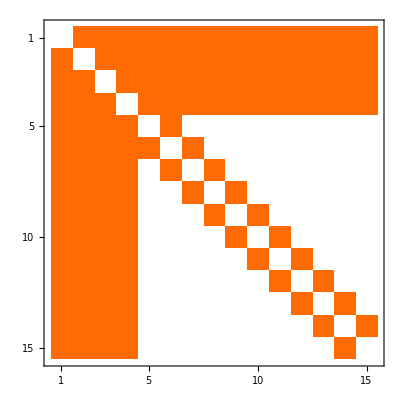
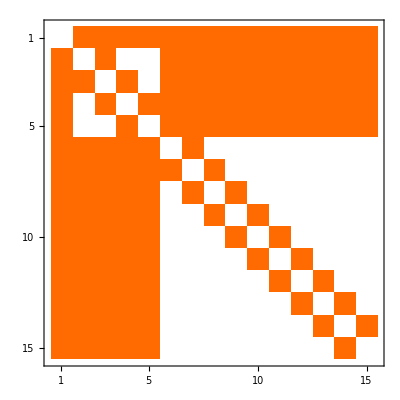
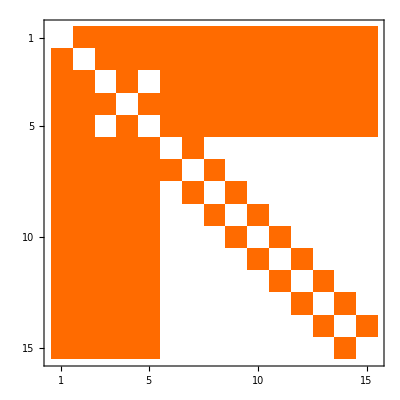
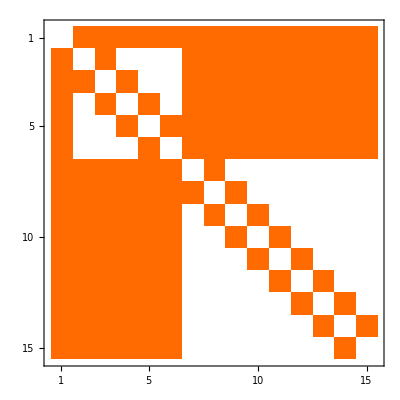
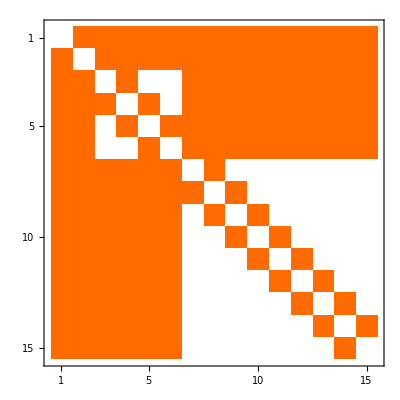
{-Graphics-True,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False,-Graphics-False}

```mathematica
Map[With[{g=FillSideDiagonal[Normal[AdjacencyMatrix[#]]]},
Labeled[MatrixPlot[g],PlanarGraphQ[AdjacencyGraph[ g]]]]&,ListSols4[15]]
```

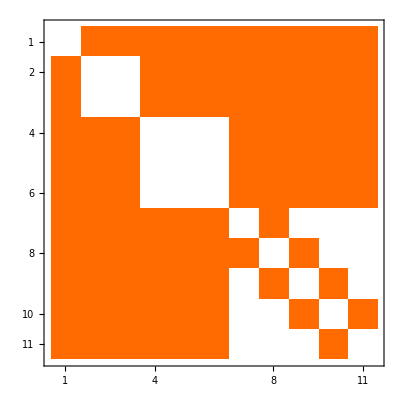

```mathematica
EdgeDelete[AdjacencyGraph[FillSideDiagonal[Normal[AdjacencyMatrix[-Graphics-]]],GraphLayout->"PlanarEmbedding"],{4<->5,5<->6,2<->3}]//AdjacencyMatrix//MatrixPlot
```

```mathematica
ChromaticPolynomial[FillSideDiagonal[Normal[AdjacencyMatrix[-Graphics-]]]//AdjacencyGraph,x]//Factor
```

(-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x (2185-1264 x+276 x^2-27 x^3+x^4)

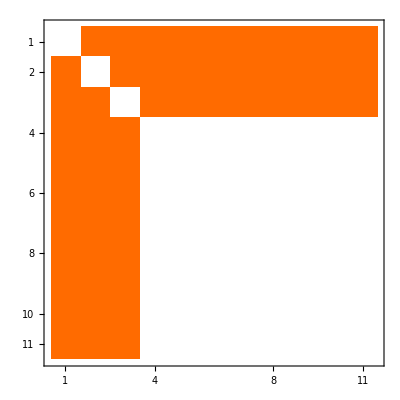
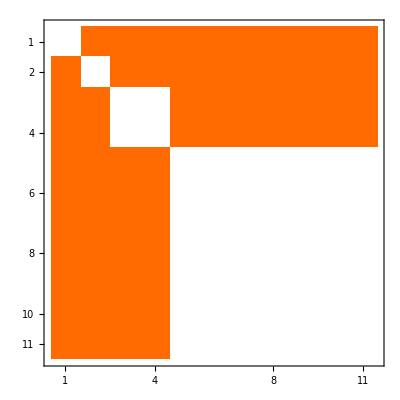
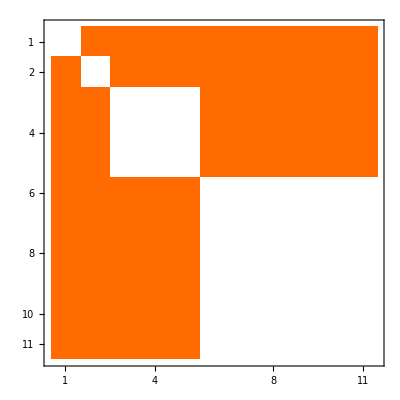
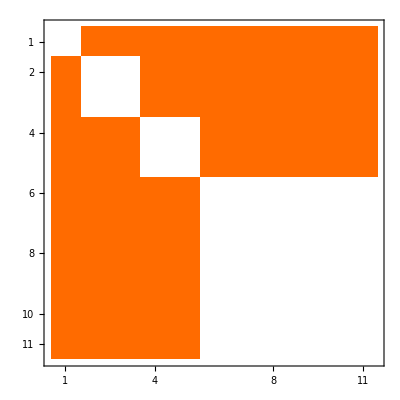
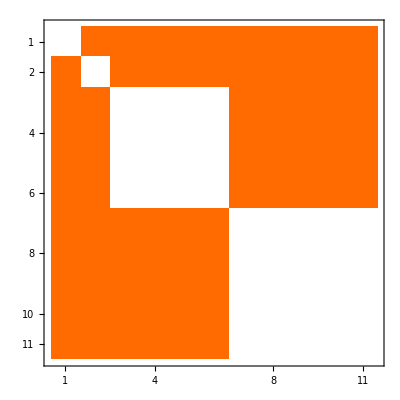
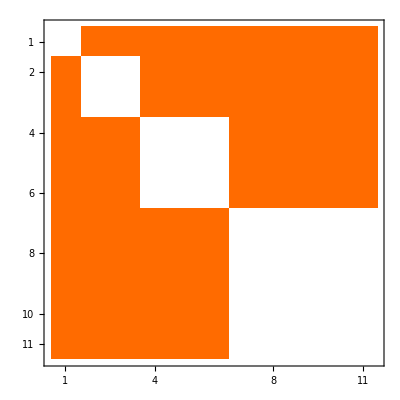
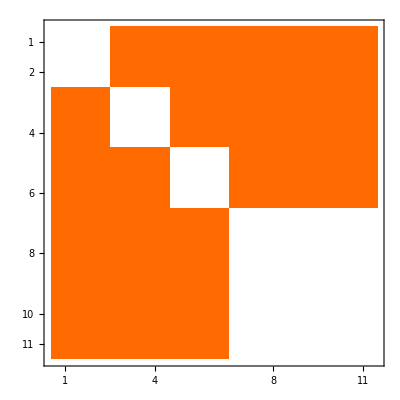
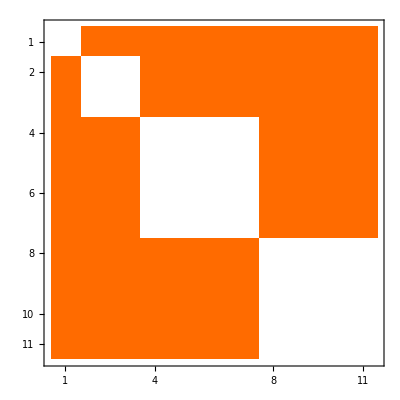

```mathematica
Map[MatrixPlot[AdjacencyMatrix[#]]&,BarelyFourColorableGraphsOfCount[11]]
```

```mathematica
Map[MaximalPlanarQ[FillSideDiagonal[AdjacencyMatrix[#]]]&,BarelyFourColorableGraphsOfCount[11]]
```

{False,False,False,False,False,False,False,False,False,False,False}

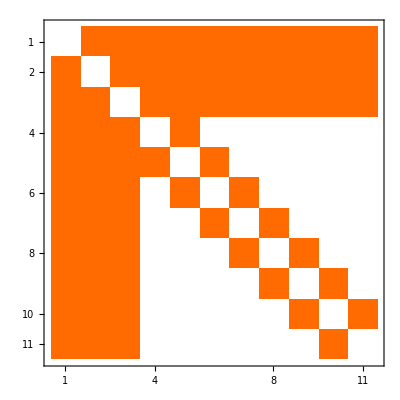
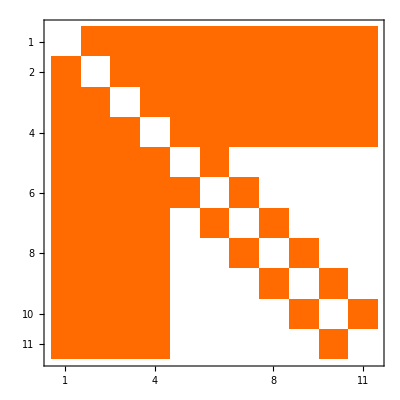
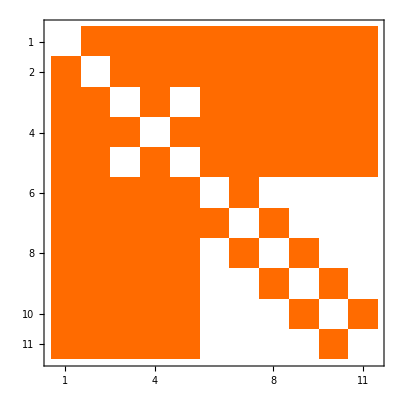
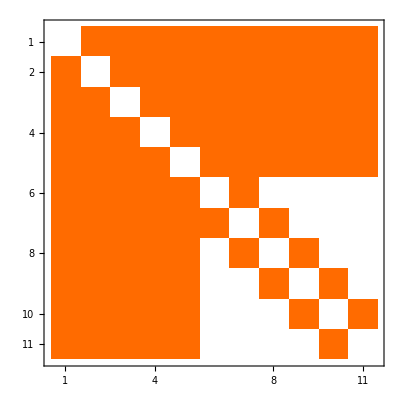
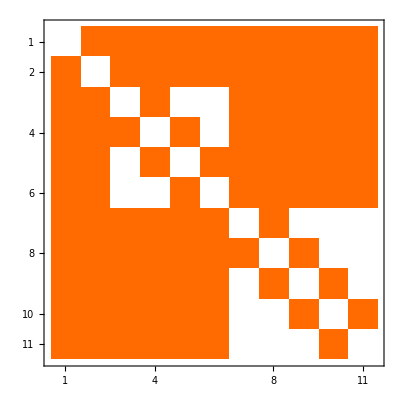
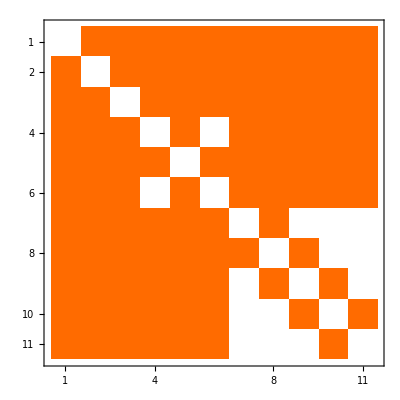
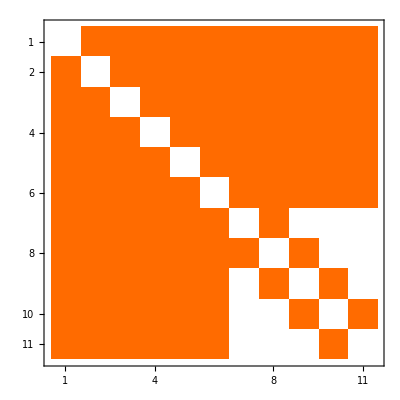
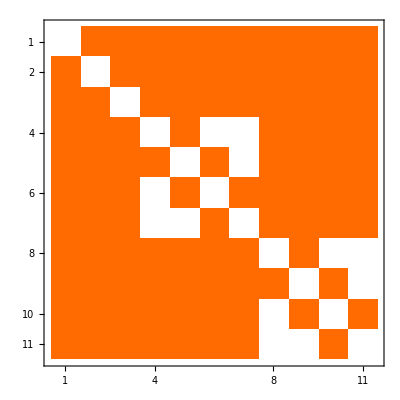

```mathematica
Map[MatrixPlot[FillSideDiagonal[AdjacencyMatrix[#]]]&,BarelyFourColorableGraphsOfCount[11]]
```

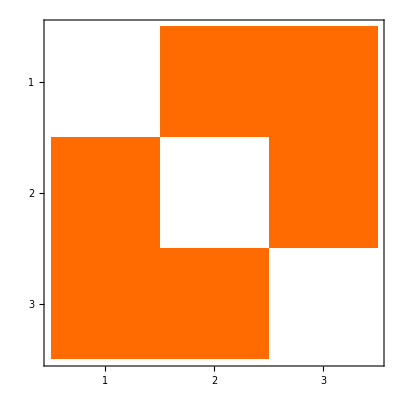
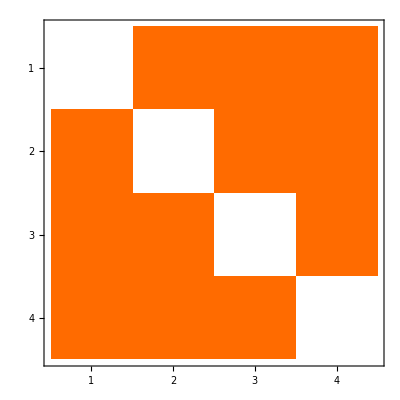
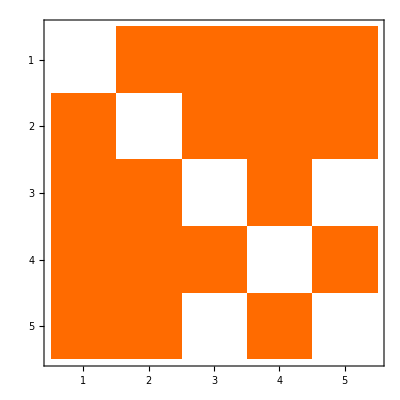
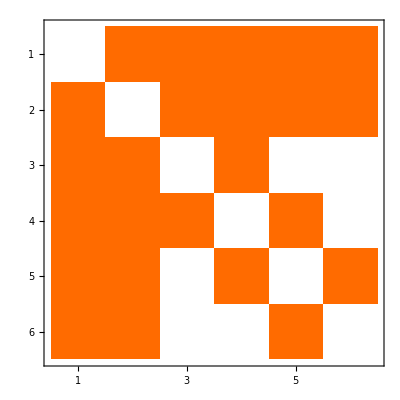
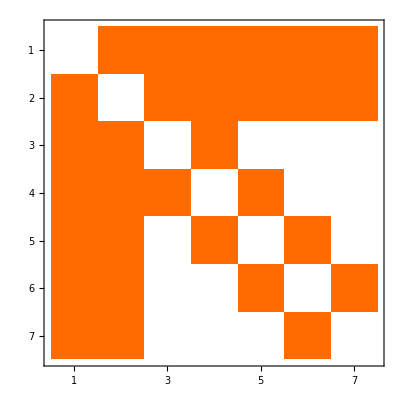
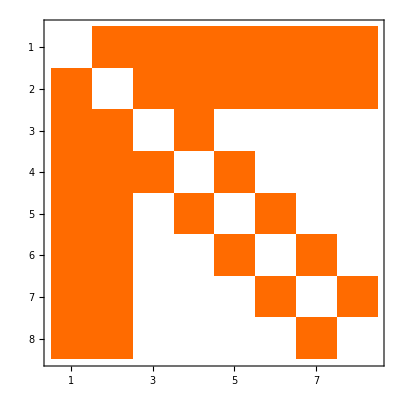
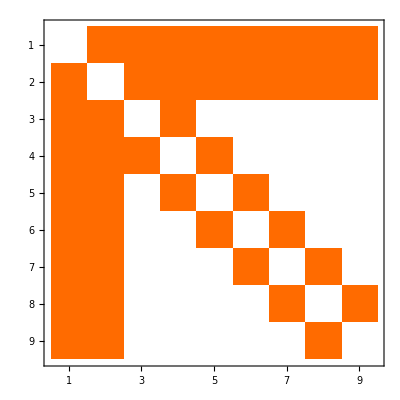
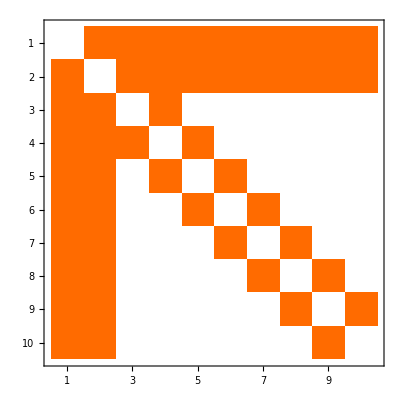
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[MatrixPlot[AdjacencyMatrix[#]]&,Table[MinimalGraph[k],{k,15}]]
```

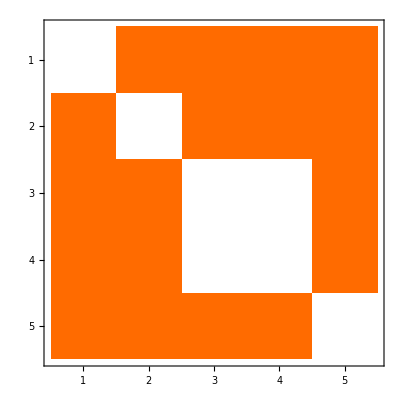
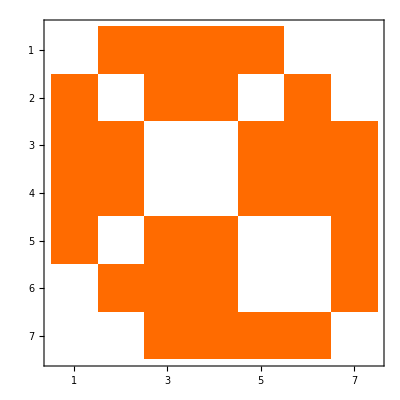
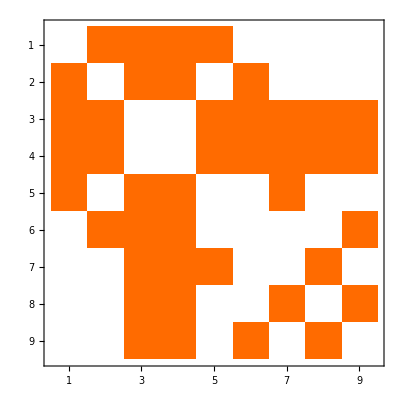
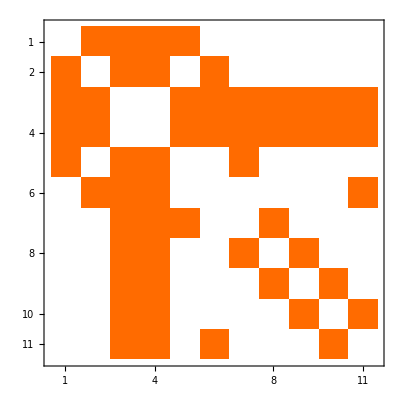
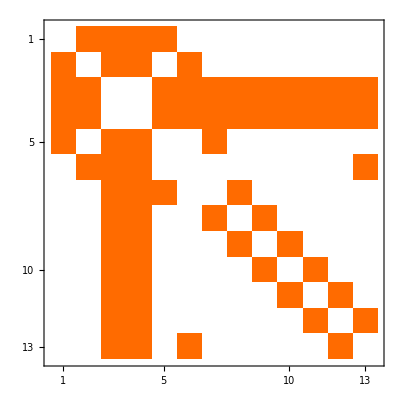
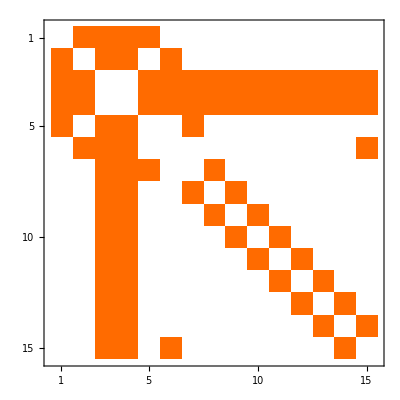
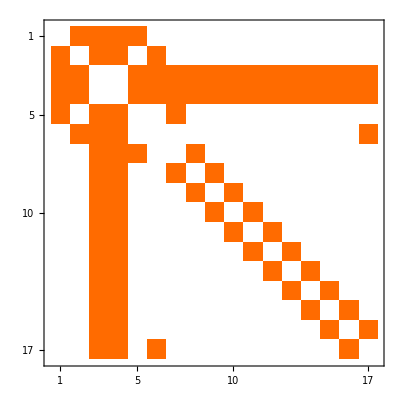
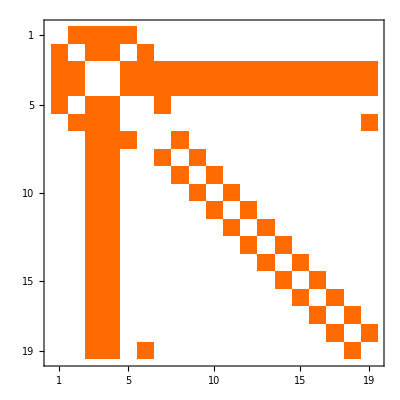

```mathematica
Map[MatrixPlot[AdjacencyMatrix[#]]&,Table[JacobsThalGraph[k],{k,1,15,2}]]
```

```mathematica
Map[Factor[CharacteristicPolynomial[AdjacencyMatrix[#],x]]&,BarelyFourColorableGraphsOfCount[10]]
```

{x^6 (1+x)^2 (-21-2 x+x^2),x^6 (1+x) (-36-28 x-x^2+x^3),x^6 (1+x) (-45-31 x-x^2+x^3),x^6 (2+x) (-30-29 x-2 x^2+x^3),x^6 (1+x) (4+x) (-12-5 x+x^2),x^6 (-72-100 x-35 x^2+x^4),x^6 (2+x)^2 (-24-4 x+x^2),x^6 (3+x)^2 (-9-6 x+x^2),x^6 (2+x) (3+x) (-18-5 x+x^2)}

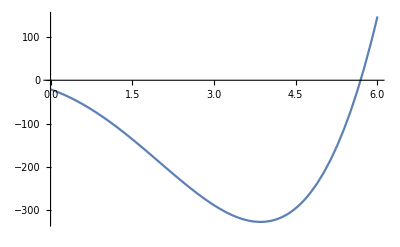

```mathematica
Plot[(1+x)^2 (-21-2 x+x^2),{x,0,6},PlotRange->All]
```

```mathematica
Map[PolynomialQ[ CharacteristicPolynomial[AdjacencyMatrix[#],xxx],xxx]&,BarelyFourColorableGraphsOfCount[10]]
```

{True,True,True,True,True,True,True,True,True}

```mathematica
Map[MatrixRank[AdjacencyMatrix[#]]&,BarelyFourColorableGraphsOfCount[10]]
```

{4,4,4,4,4,4,4,4,4}

```mathematica
Map[Plot[PolynomialQ[ CharacteristicPolynomial[AdjacencyMatrix[#],xxx],xxx],{xxx,0,6},PlotRange->All]&,BarelyFourColorableGraphsOfCount[10]]
```

General::ivar: 0.000122571 is not a valid variable.

General::ivar: 0.122572 is not a valid variable.

General::ivar: 0.245021 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[N[Eigenvalues[AdjacencyMatrix[#]]]&,BarelyFourColorableGraphsOfCount[10]]
```

{{5.69042,-3.69042,-1.,-1.,0.,0.,0.,0.,0.,0.},{6.32588,-3.84631,-1.47958,-1.,0.,0.,0.,0.,0.,0.},{6.66459,-3.95913,-1.70545,-1.,0.,0.,0.,0.,0.,0.},{6.86272,-3.67235,-2.,-1.19037,0.,0.,0.,0.,0.,0.},{6.772,-4.,-1.772,-1.,0.,0.,0.,0.,0.,0.},{7.1062,-3.52503,-2.36668,-1.21449,0.,0.,0.,0.,0.,0.},{7.2915,-3.2915,-2.,-2.,0.,0.,0.,0.,0.,0.},{7.24264,-3.,-3.,-1.24264,0.,0.,0.,0.,0.,0.},{7.42443,-3.,-2.42443,-2.,0.,0.,0.,0.,0.,0.}}

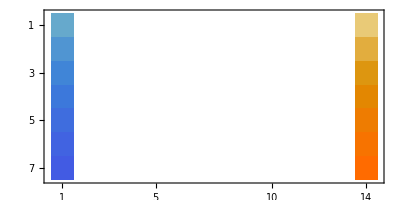
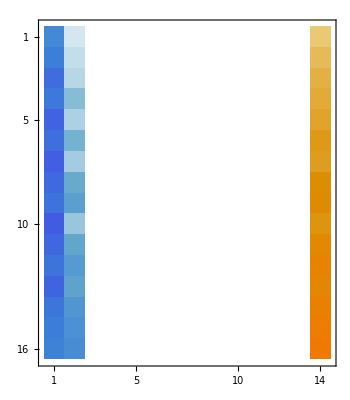
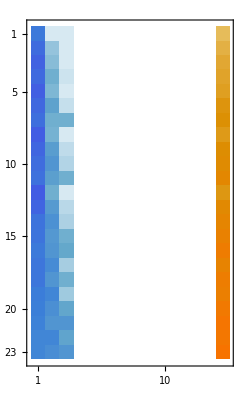
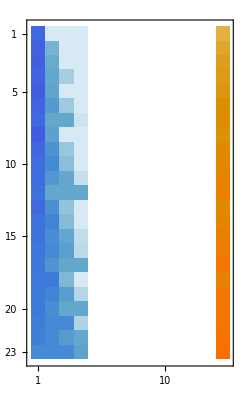
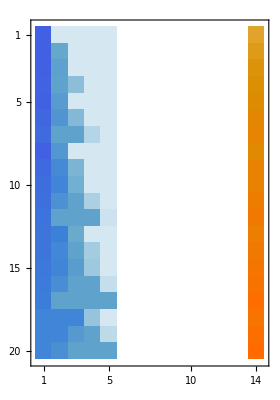
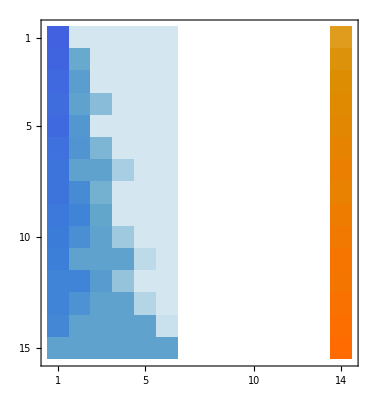
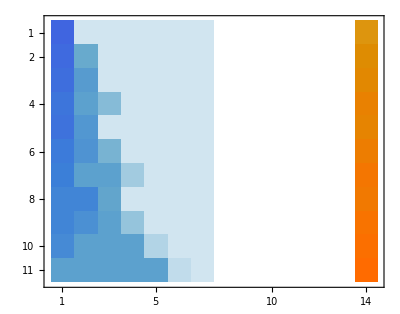
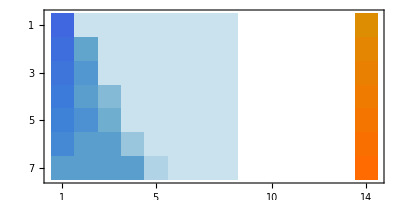
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Map[Sort[N[Eigenvalues[AdjacencyMatrix[#]]]]&,BarelyNColorableGraphsOfCount[14,n]]//MatrixPlot,{n,1,14}]
```

```mathematica
Table[n->Map[MatrixRank[N[Eigenvectors[AdjacencyMatrix[#]]]]&,BarelyNColorableGraphsOfCount[9,n]],{n,3,8}]
```

{3→{9,9,9,9,9,9,9},4→{9,9,9,9,9,9},5→{9,9,9,9,9},6→{9,9,9},7→{9,9},8→{9}}

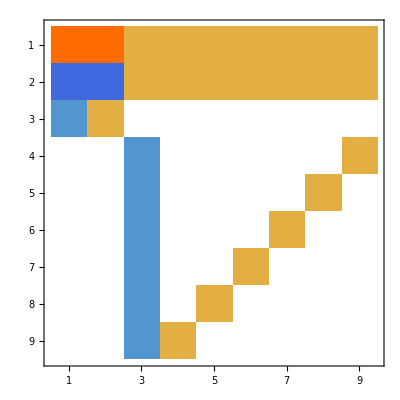
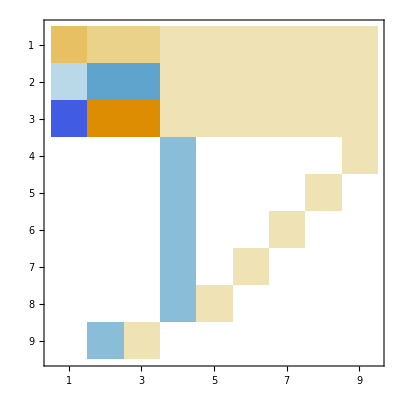
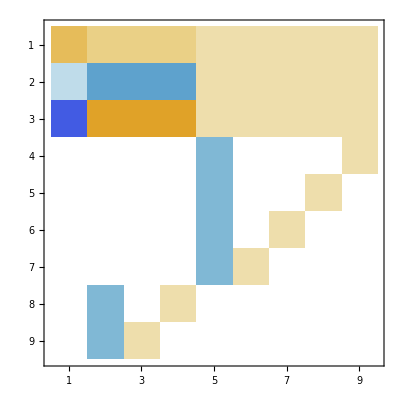
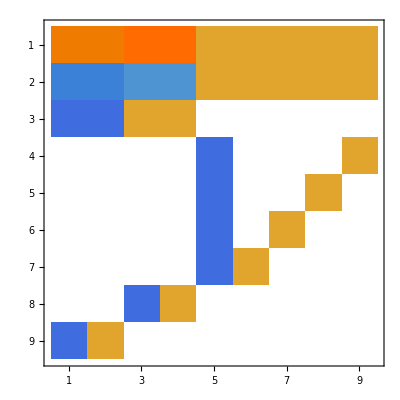
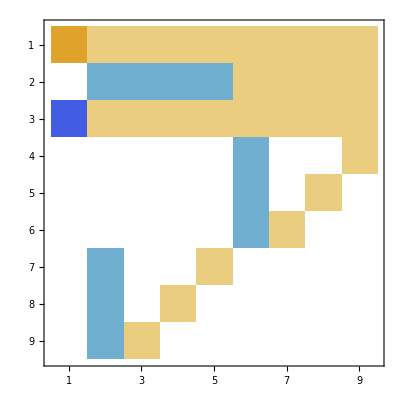
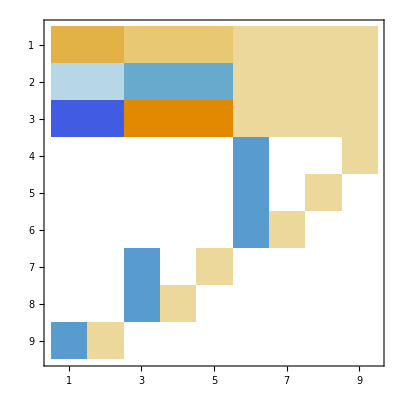
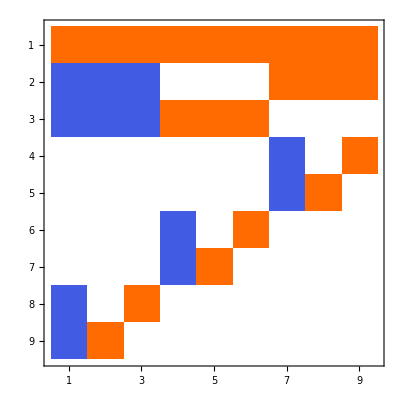
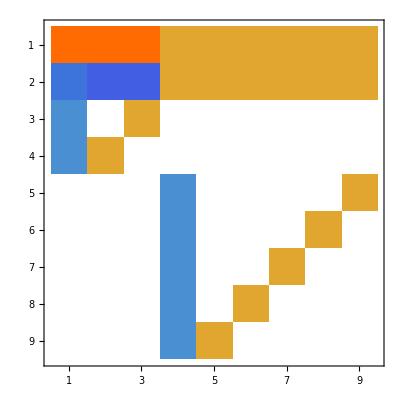
{3→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},4→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},5→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},6→{-Graphics-,-Graphics-,-Graphics-},7→{-Graphics-,-Graphics-},8→{-Graphics-}}

```mathematica
Table[n->Map[MatrixPlot[N[Eigenvectors[AdjacencyMatrix[#]]]]&,BarelyNColorableGraphsOfCount[9,n]],{n,3,8}]
```

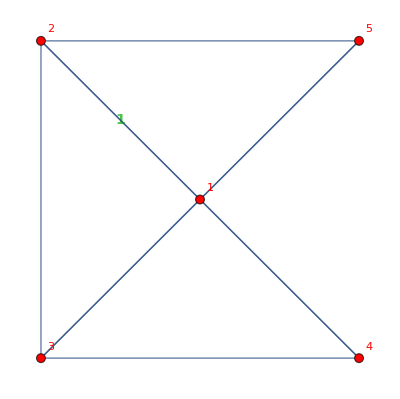
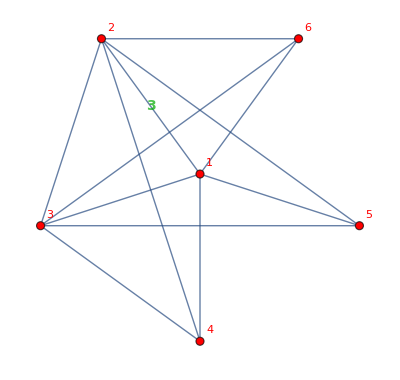
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[First[BarelyNColorableGraphsOfCount[k,4]],{k,5,10}]
```

```mathematica
Map[MatrixRank[AdjacencyMatrix[#]]&,Table[Last[BarelyNColorableGraphsOfCount[k,3]],{k,5,10}]]//ListLinePlot
```

-Graphics-

```mathematica
Map[Mod[MatrixRank[AdjacencyMatrix[#]],4]&,Table[MinimalGraph[k],{k,3,30}]]//ListLinePlot
```

-Graphics-

```mathematica
Map[Mod[MatrixRank[AdjacencyMatrix[#]],4]&,Table[JacobsThalGraph[k],{k,3,30}]]//ListLinePlot
```

-Graphics-

```mathematica
Map[MatrixPlot[N[Eigenvectors[AdjacencyMatrix[#]]]]&,Table[JacobsThalGraph[k],{k,3,15}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[N[Eigenvalues[AdjacencyMatrix[#]]]&,BarelyFiveColorableGraphsOfCount[14]]//MatrixPlot
```

-Graphics-

```mathematica
Map[ListLinePlot[N[Eigenvalues[AdjacencyMatrix[#]]]]&,BarelyFourColorableGraphsOfCount[10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ListLinePlot[N[Eigenvalues[AdjacencyMatrix[#]]]]&,BarelyFiveColorableGraphsOfCount[10]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
g=EdgeList[EdgeAdd[CompleteGraph[4,VertexLabels->"Name",GraphLayout->"TutteEmbedding"],{1<->5,4<->5,3<->5,3<->6,2<->6,1<->6,2<->7,3<->7,4<->7}]]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->4,2<->6,2<->7,3<->4,3<->5,3<->6,3<->7,4<->5,4<->7}

```mathematica
g2=Sort[(g/.{2->bolla,5->boenga})/.{bolla->5,boenga->2}]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,3<->2,3<->4,3<->6,3<->7,4<->2,4<->7,5<->3,5<->4,5<->6,5<->7}

```mathematica
Swap[mat_,c1_,c2_]:=Block[{result=mat,l=Length[mat],temp},
Table[
temp=result[[c1,i]];
result[[c1,i]]=result[[c2,i]];
result[[c2,i]]=temp;

temp=result[[i,c1]];
result[[i,c1]]=result[[i,c2]];
result[[i,c2]]=temp;
,{i,l}];
result
]
```

```mathematica
AdjacencyMatrix[g2]
```

SparseArray[<30>, {7, 7}]

```mathematica
MatrixPlot[AdjacencyMatrix[g2].AdjacencyMatrix[First[BarelyFourColorableGraphsOfCount[7]]]]
```

-Graphics-

```mathematica
Sort[AdjacencyMatrix[g2]//Normal]
```

{{0,0,1,1,1,0,0},{0,1,1,1,1,1,0},{1,0,1,0,1,0,0},{1,0,1,1,0,0,0},{1,0,1,1,0,1,1},{1,1,0,1,1,1,1},{1,1,1,0,1,0,1}}

```mathematica
Map[MatrixPlot[AdjacencyMatrix[#]]&,Flatten[Table[Map[First,Tally[CalcMinGraphs[CompleteGraph[3,VertexLabels->"Name"],{{1,2,3}},l],IsomorphicGraphQ]],{l,2,4}]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[MaximalPlanarQ[#]&,Flatten[Table[Map[First,Tally[CalcMinGraphs[CompleteGraph[3,VertexLabels->"Name"],{{1,2,3}},l],IsomorphicGraphQ]],{l,2,4}]]]
```

{True,False,True,False,False,True,True,True}